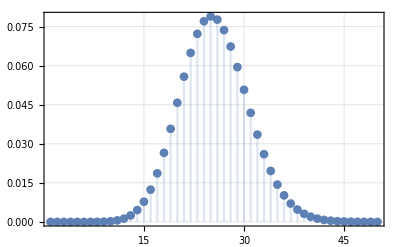

```mathematica
p = 0.00001;
nn = 2560000;

DiscretePlot[Table[PDF[BinomialDistribution[n,p],k],{n,{nn}}]//Evaluate,{k,50},PlotRange->All,PlotMarkers->Automatic, Frame -> True, GridLines->Automatic]

(*
DiscretePlot[Table[PDF[BinomialDistribution[n,0.002],k],{n,{100000}}]//Evaluate,{k,400},PlotRange->All,PlotMarkers->Automatic, Frame -> True, GridLines->Automatic]

DiscretePlot[Table[PDF[BinomialDistribution[n,0.002],k],{n,{4096}}]//Evaluate,{k,20},PlotRange->All,PlotMarkers->Automatic, Frame -> True, GridLines->Automatic]
*)
```